```mathematica
Clear[ndf,pdf,cdf]
ndf[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
(*cdf=Function[{θ,α},Evaluate[Integrate[2*π*ndf[θ,α]*Cos[θ]*Sin[θ],θ]]]*)
cdf[θ_,α_]:=(1-Cos[θ]^2)/(1+Cos[θ]^2*(α^2-1))
pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
pdfCos[cosθ_,α_]:=α^2/(π*(cosθ^2*(α^2-1)+1)^2)*cosθ
```

Compute the difference of the PDFs of 2 neighbor pixels

```mathematica
(*Clear[α]
Integrate[2*π*(ndf[θ,α] - ndf[θ-β,α])*Cos[θ]*Sin[θ],θ]*)
```

```mathematica
ndf2[μ_,α_]:=α^2/(π*(μ^2*(α^2-1)+1)^2)
test[μ0_,α_]:=cdf[μ0,α]+ NIntegrate[2*π*(ndf2[μ,α] - ndf2[μ-μ0,α])*μ*√(1-μ^2),{μ,μ0,0}]
```

```mathematica
Manipulate[Plot[{test[μ0,α],cdf[μ0,α]},{α,0,1},PlotRange->{0,1}],{μ0,1,0}]
```

```mathematica
test[θ0_,α_]:=cdf[Cos[θ0],α]+ NIntegrate[2*π*(ndf[θ,α] - ndf[θ-θ0,α])*Cos[θ]*Sin[θ],{θ,θ0,π/2}]
Manipulate[Plot[{test[θ,α],cdf[Cos[θ],α]},{α,0,1},PlotRange->{-1,1}],{θ,0.01,π/2}]
```

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

Test with subtraction of the 2 lobes:

```mathematica
Manipulate[Show[Plot[(pdf[θ,α]*Sin[θ])/cdf[θ0/2,α]-(pdf[θ0-θ,α]*Sin[θ0-θ])/cdf[θ0/2,α],{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

Test with multiplication of the 2 lobes (true correlation):

```mathematica
Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

Showing angular correlation visually:

```mathematica
ColorData[97,"ColorList"]
ColorData[97][1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
defaultBlue=ColorData[97][1];
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]}, 4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],α]/cdf[θ0/2,α]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],α]/cdf[θ0/2,α]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],α]*pdf[Abs[(π/4+θ0/2)-θ],α])/cdf[θ0/2,α]^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ],{θ,0,π/2},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
```

```mathematica
(*Clear[α]
Integrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,θ]*)
```

```mathematica
(*Manipulate[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[NIntegrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0/2}],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
(*Manipulate[Plot[NIntegrate[2*π*(ndf[θ,α]*Cos[θ]-ndf[θ-θ0,α]*Cos[θ-θ0])*Sin[θ],{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]*)
Manipulate[Plot[NIntegrate[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0/2}],{α,0,1},PlotRange->{0,1}],{{θ0,π/10},0,π/2}]
```

Show the correlation

```mathematica
(*Manipulate[Show[Plot[ndf[θ,α]*Cos[θ]*ndf[θ-θ0,α]*Cos[θ-θ0],{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,0.05},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
(*Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/cdf[θ0,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/π)^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[Show[Plot[(pdf[θ,α]*pdf[θ0-θ,α])/cdf[θ0/2,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,((√2)/π)^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((ndf(θ_0/2,α) cos(θ_0/2)sin(θ_0/2))/(cdf(θ_0/2,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (ndf(π/4,1) cos(π/4)sin(π/4))/(cdf(π/2,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/π

```mathematica
(ndf[π/4,1]*Cos[π/4]*Sin[π/4])/cdf[π/4,1]
pdf[π/4,1]/cdf[π/4,1]
```

1/π

(√2)/π

```mathematica
Solve[(pdf[θ,α]*Sin[θ])/cdf[θ,α]==c,α]
```

{{α→-(ⅈ √c √π (-1+Cos[θ]^2))/(√(c π Cos[θ]^2-c π Cos[θ]^4-Cos[θ] Sin[θ]))},{α→(ⅈ √c √π (-1+Cos[θ]^2))/(√(c π Cos[θ]^2-c π Cos[θ]^4-Cos[θ] Sin[θ]))}}

```mathematica
Clear[c]
Solve[pdf[θ,α]/cdf[θ,α]==c,α]
```

{{α→-(ⅈ √c √π (-1+Cos[θ]^2))/(√(-Cos[θ]+c π Cos[θ]^2-c π Cos[θ]^4))},{α→(ⅈ √c √π (-1+Cos[θ]^2))/(√(-Cos[θ]+c π Cos[θ]^2-c π Cos[θ]^4))}}

```mathematica
(*cmax = 1/π;
c=cmax/(8π);
sqAlpha[θ_]:=(c*Cos[θ]^2)/(Sin[θ]-c*Sin[θ]^2)
sqAlpha[θ_]:=(-π*cmax* Sin[θ]^4)/(π*cmax* Cos[θ]^2-π*cmax* Cos[θ]^4-Cos[θ]*Sin[θ])*)
```

```mathematica
cmax=(√2)/π;
c=cmax * π;
(*sqAlpha[θ_]:=(-c*Sin[θ]^4)/(c* Cos[θ]^2-c* Cos[θ]^4-Cos[θ]*Sin[θ]) with sin(θ) *)
sqAlpha[θ_]:=(-c*Sin[θ]^4)/(c* Cos[θ]^2-c* Cos[θ]^4-Cos[θ])
```

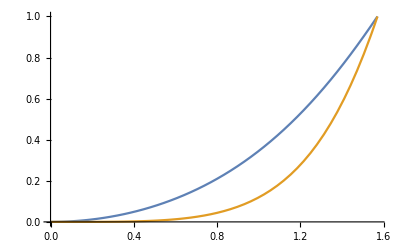

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
```

```mathematica
mipMax=8;
(*mu[mip_]:=1-1/3 2^(2(mip-mipMax))   Solid angles yields θ > π/2*)
mu[mip_]:=1/(√(1+2^(2(mip-mipMax))))
sqRoughnessFromMip[mip_]:=sqAlpha[ ArcCos[mu[mip]] ]

mu[8]
2*ArcCos[mu[8]]
Table[N[sqRoughnessFromMip[mip]],{mip,0,mipMax}]
```

1/(√2)

π/2

{3.29272×10^-10,5.26833×10^-9,8.42919×10^-8,1.34859×10^-6,0.0000215718,0.000344773,0.0054869,0.0846641,1.}

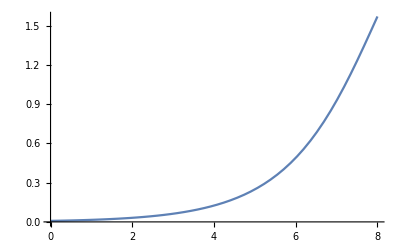

```mathematica
Plot[2*ArcCos[mu[mip]],{mip,0,mipMax},PlotRange->{0,π/2}]
```

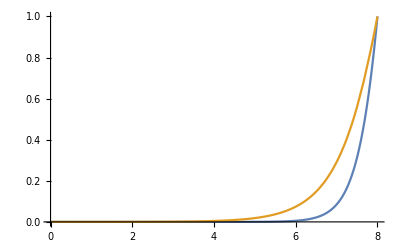

```mathematica
Plot[{sqRoughnessFromMip[mip],√sqRoughnessFromMip[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

Compute the correlation between 2 opposed NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

It would look like we’re doing the same thing all over again but the normalization by pdf(0,α) makes much more sense than dividing by the cdf!

Showing angular correlation visually:

```mathematica
defaultBlue=ColorData[97][1];
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],α]/pdf[0,α]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],α]/pdf[0,α]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],α]*pdf[Abs[(π/4+θ0/2)-θ],α])/pdf[0,α]^2*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

Plotting angular correlation as a function of angle:

```mathematica
(*Manipulate[Show[Plot[((pdf[θ,α]*Sin[θ])*(pdf[θ0-θ,α]*Sin[θ0-θ]))/pdf[0,α]^2,{θ,0,θ0},PlotRange->Full],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]*)
Manipulate[Show[Plot[(pdf[θ,α]*pdf[θ0-θ,α])/pdf[0,α]^2,{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/(√2))^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((pdf(θ_0/2,α))/(pdf(0,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (pdf(π/4,1))/(pdf(0,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/(√2)

```mathematica
(ndf[π/4,1]*Cos[π/4])/pdf[0,1]
pdf[π/4,1]/pdf[0,1]
```

1/(√2)

1/(√2)

```mathematica
Clear[c,θ,α]
(*Solve[pdf[θ,α]/pdf[0,α]==c,α]*)
Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,α]
```

{{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))}}

```mathematica
Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,b]
```

{{b→-1/2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))-1/2 √(-2/(-1+α^2)+(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))-(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))-((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4))-(2 α^4)/(c (-1+α^2)^2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))))},{b→-1/2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))+1/2 √(-2/(-1+α^2)+(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))-(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))-((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4))-(2 α^4)/(c (-1+α^2)^2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))))},{b→1/2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))-1/2 √(-2/(-1+α^2)+(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))-(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))-((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4))+(2 α^4)/(c (-1+α^2)^2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))))},{b→1/2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))+1/2 √(-2/(-1+α^2)+(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))-(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))-((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4))+(2 α^4)/(c (-1+α^2)^2 √(-2/(-1+α^2)-(2 (-c+c α^2))/(3 (-c+2 c α^2-c α^4))+(16 2^(1/3) (c^2-2 c^2 α^2+c^2 α^4))/(3 (-c+2 c α^2-c α^4) (-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))+((-128 c^3+384 c^3 α^2-384 c^3 α^4+128 c^3 α^6-27 c α^8+54 c α^10-27 c α^12+3 √3 √(256 c^4 α^8-1280 c^4 α^10+2560 c^4 α^12-2560 c^4 α^14+27 c^2 α^16+1280 c^4 α^16-108 c^2 α^18-256 c^4 α^18+162 c^2 α^20-108 c^2 α^22+27 c^2 α^24))^(1/3))/(3 2^(1/3) (-c+2 c α^2-c α^4)))))}}

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
```

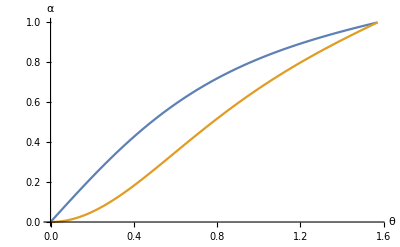

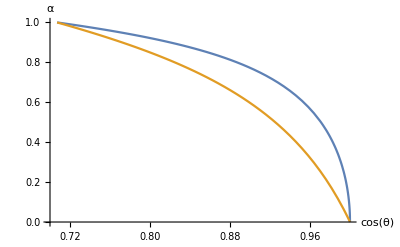

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqAlphaMu[μ],sqAlphaMu[μ]},{μ,1/(√2),1},PlotRange->{{0.70,1},{0,1}},AxesLabel->{"cos(θ)","α"}]
```

2/3

1.68214

{0.00733224,0.0146636,0.0293201,0.0585836,0.116718,0.229944,0.434916,0.731737,1.02718}

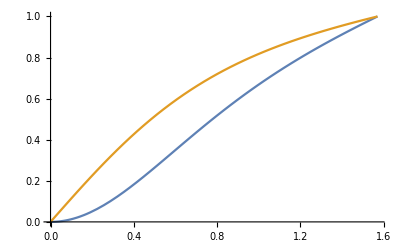

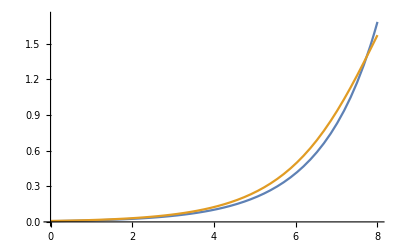

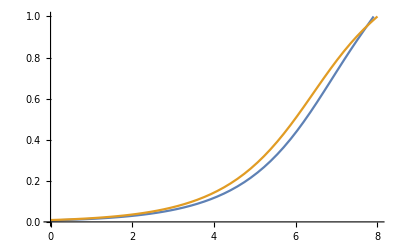

```mathematica
mipMax=8;
mu[mip_]:=1-1/3 2^(2(mip-mipMax))   (*Solid angles yields θ > π/2*)
mu2[mip_]:=1/(√(1+2^(2(mip-mipMax))))
sqRoughnessFromMip[mip_]:=sqAlpha[ArcCos[mu[mip]] ]
sqRoughnessFromMip2[mip_]:=sqAlpha[ArcCos[mu2[mip]] ]
mu[8]
N[2*ArcCos[mu[8]]]
Table[N[√sqRoughnessFromMip[mip]],{mip,0,mipMax}]
Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
Plot[{2*ArcCos[mu[mip]],2*ArcCos[mu2[mip]]},{mip,0,mipMax},PlotRange->{0,1.1*π/2}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip2[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

```mathematica
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]*pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]])/pdf[0,√sqAlpha[θ0/2]]^2*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{θ0,π/2},0.001,π/2}]
```

Fitting

The expression to get μ from roughness is a nightmare to invert so let’s do a curve fitting instead...

{{1.,0.707107},{0.995845,0.710036},{0.991663,0.712965},{0.987454,0.715894},{0.983216,0.718823},{0.978948,0.721751},{0.97465,0.72468},{0.970321,0.727609},{0.965958,0.730538},{0.961562,0.733467},{0.957132,0.736396},{0.952665,0.739325},{0.948161,0.742254},{0.943619,0.745183},{0.939037,0.748112},{0.934415,0.751041},{0.92975,0.75397},{0.925042,0.756899},{0.920289,0.759828},{0.915489,0.762756},{0.910642,0.765685},{0.905746,0.768614},{0.900799,0.771543},{0.895799,0.774472},{0.890746,0.777401},{0.885636,0.78033},{0.880469,0.783259},{0.875243,0.786188},{0.869956,0.789117},{0.864605,0.792046},{0.859189,0.794975},{0.853706,0.797904},{0.848154,0.800833},{0.84253,0.803762},{0.836832,0.80669},{0.831058,0.809619},{0.825206,0.812548},{0.819272,0.815477},{0.813254,0.818406},{0.80715,0.821335},{0.800956,0.824264},{0.794669,0.827193},{0.788287,0.830122},{0.781806,0.833051},{0.775224,0.83598},{0.768535,0.838909},{0.761738,0.841838},{0.754828,0.844767},{0.747801,0.847696},{0.740653,0.850624},{0.73338,0.853553},{0.725978,0.856482},{0.718442,0.859411},{0.710767,0.86234},{0.702948,0.865269},{0.694979,0.868198},{0.686856,0.871127},{0.678573,0.874056},{0.670123,0.876985},{0.6615,0.879914},{0.652698,0.882843},{0.64371,0.885772},{0.634528,0.888701},{0.625144,0.89163},{0.615552,0.894558},{0.605741,0.897487},{0.595704,0.900416},{0.58543,0.903345},{0.574911,0.906274},{0.564135,0.909203},{0.553092,0.912132},{0.541769,0.915061},{0.530155,0.91799},{0.518237,0.920919},{0.506001,0.923848},{0.493432,0.926777},{0.480515,0.929706},{0.467234,0.932635},{0.45357,0.935563},{0.439506,0.938492},{0.425022,0.941421},{0.410097,0.94435},{0.394707,0.947279},{0.37883,0.950208},{0.36244,0.953137},{0.345509,0.956066},{0.328008,0.958995},{0.309905,0.961924},{0.291167,0.964853},{0.271756,0.967782},{0.251635,0.970711},{0.23076,0.97364},{0.209086,0.976569},{0.186564,0.979497},{0.163139,0.982426},{0.138754,0.985355},{0.113346,0.988284},{0.0868448,0.991213},{0.0591763,0.994142},{0.030258,0.997071},{0.,1.}}

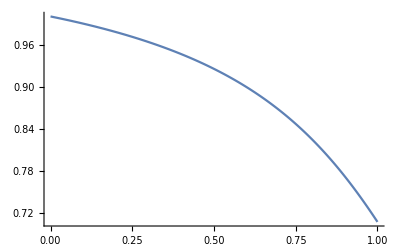

```mathematica
data=Table[{ N[sqAlphaMu[μ]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}]
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(1.2547-1.87042 x+0.720235 x^2)/(1.2547-1.75224 x+0.645329 x^2)]

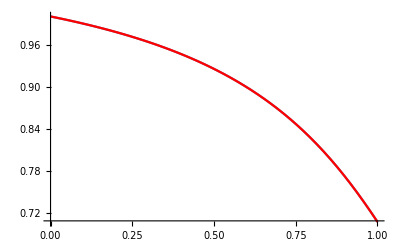

1.00011

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)

f0=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f0[x],{x,0,1},PlotStyle->Red]]
√2 f0[1]
```

3D Lobes Inter-Penetration Modeling

Here we’re attempting to port the same reflection to the 3D realm. The idea is measuring how much 2 adjacent lobes interpenetrate each other depending on the separation angle (i.e. the lobe’s aperture angle) and the roughness of the lobe.
Once again we “normalize a lobe” by dividing by its largest amplitude at θ=0 and we’re looking to compute the integral:

	I=∫_-θ_0^θ_0 ∫_0^(π/2) (D(θ,α) D( θ', α ) cos(θ)  cos(θ') sin(θ))/(D( 0, α ))^2 ⅆθⅆϕ

Here, cos(θ')= sin( θ ) cos( ϕ ) sin( θ_0) + cos( θ ) cos( θ_0 ) and θ_0 is the cone’s aperture angle.

```mathematica
cosAngleChange[θ_,ϕ_,γ_]:=Sin[θ]*Cos[ϕ]*Sin[γ]+Cos[θ]*Cos[γ]
penelobe[θ_,ϕ_,γ_,α_]:=pdf[θ,α]*pdfCos[cosAngleChange[θ,ϕ,γ],α]
```

```mathematica
γ=0.1
α=0.05
NIntegrate[penelobe[θ,ϕ,γ,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}]
```

0.1

0.05

7.25895

1.0472

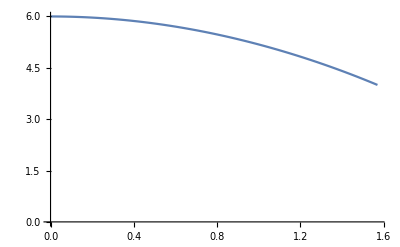

```mathematica
lobeSeparationAngle[θ0_]:=ArcCos[(Cos[θ0]-Cos[θ0]^2)/(1-Cos[θ0]^2)]
lobesCount[θ0_]:=(2π)/lobeSeparationAngle[Max[0.0001,θ0]]
lobeSeparationAngle[0.0001]
Plot[lobesCount[θ0],{θ0,0,π/2},PlotRange->{0,6}]
```

Here it’s interesting to realize the limit converges to 6 possible neighbors, I would have expected an unlimited amount of neighbors as the lobes get thinner and thinner...
But after all, if you zoom in on things, even though they’re getting very small, maybe you always end up with 6 neighbor lobes no matter what.

The other extremity of 4 lobes when the angle is π/2is totally expected, on the other hand: each face of the cube has exactly 4 neighbor faces, thus 4 neighbor lobes.

```mathematica
Manipulate[lobesCount[θ0]*NIntegrate[penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

NIntegrate::inumr: The integrand 6.47545\ penelobe[θ, ϕ, π/10, 0.9]\ Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.5608}, {-1.5708, 1.5708}}.

```mathematica
Manipulate[NIntegrate[penelobe[θ,ϕ,θ0,α]/pdf[0,α]^2*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[lobesCount[θ0]*NIntegrate[penelobe[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.0001,1}]
```

```mathematica
Manipulate[NIntegrate[pdf[θ,α]/pdf[0,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{α,0.9},0.001,1}]
```

```mathematica
Manipulate[lobesCount[θ0]/2*NIntegrate[pdf[θ,α]*Sin[θ],{θ,0,π/2-0.01},{ϕ,-π/2,π/2}],{{θ0,π/10},0.001,π/2},{{α,0.9},0.0001,1}]
```

```mathematica
Manipulate[ParametricPlot3D[{
pdf[θ,α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]},
pdfCos[cosAngleChange[θ,ϕ,γ],α]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]},
Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]*{Sin[θ]*Cos[ϕ], Sin[θ]*Sin[ϕ], Cos[θ]}
},{θ,0,π/2},{ϕ,-π/2,π/2},PlotRange->{{0,0.5},{-0.25,0.25},{0,0.5}},AxesLabel->{"x","y","z"},PlotStyle->{Opacity[0.125],Opacity[0.125],Directive[Red,Opacity[1]]}],{{α,1},0.0001,1},{{γ,π/2},0.0001,π/2}]
```

```mathematica
penelobeMin[θ_,ϕ_,γ_,α_]:=Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]
Manipulate[NIntegrate[penelobeMin[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2},{ϕ,-π/2,π/2}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision],{{θ0,π/2},0.001,π/2},{{α,1},0.0001,1}]
```

```mathematica
SetDirectory["D:\\Workspaces\\Patapom.com\\Web\\blog\\patapom\\docs\\BRDF"]; 
countX=128;
countY=64;
```

```mathematica
(*ta=ParallelTable[{N[θ0],N[α],
NIntegrate[penelobeMin[θ,ϕ,θ0,α]*Sin[θ],{θ,0,π/2},{ϕ,-π/2,π/2}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision]
}
,{θ0,0,π/2,(π/2)/countX}
,{α,0.001,1,(1-0.001)/countY}]
Export["VolumeInterPenetration_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv",ta,"CSV"];*)
```

```mathematica
ta=Import["VolumeInterPenetration_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv","CSV"];
ta=ToExpression[ta]
```

{{{0.,0.001,0.500004888822118},{0.,0.0166094,0.499987470449681},{0.,0.0322188,0.499997428711909},{0.,0.0478281,0.500002007227455},{0.,0.0634375,0.499959181225379},55,{0.,0.937563,0.49999124339241},{0.,0.953172,0.499995427933608},{0.,0.968781,0.49999842603266},{0.,0.984391,0.500000213909253},{0.,1.,0.5000008023512}},127,{1}}
 |  |  |  |

```mathematica
ListPlot3D[Flatten[ta,1],PlotRange->Full]
```

-Graphics3D-

```mathematica
ta2=Table[ta[[x]][[y]] * {1,1,lobesCount[ta[[x]][[y]][[1]]]/lobesCount[π/2]},{x,1,countX+1},{y,1,countY+1}];
ta3=Table[ta[[x]][[y]] [[3]],{x,1,countX+1},{y,1,countY+1}]; (* This table doesn't account for lobes increase with angle *)
ta3=Table[lobesCount[ta[[x]][[y]][[1]]]/lobesCount[π/2]*ta[[x]][[y]] [[3]],{x,1,countX+1},{y,1,countY+1}];  (* This table will increase the amount of lobes from 4 at π/2 to 6 at 0° *)
roughnessFunction=ListInterpolation[ta3,{{0,π/2},{0,1}}]
ta[[countX+1]][[countY+1]]
ref=ta2[[countX+1]][[countY+1]][[3]]
```

InterpolatingFunction[{{0., 1.5708}, {0., 1.}}, <>]

{1.5708,1.,0.292971659095527}

0.292972

```mathematica
Show[(*ListPlot3D[Flatten[ta2,1],PlotRange->Full,AxesLabel->{"θ","α","Penetration"}],*)
Plot3D[roughnessFunction[θ,α],{θ,0,π/2},{α,0,1}],
Plot3D[ref,{θ,0,π/2},{α,0,1},PlotStyle->Darker[Green,0.1]]]
```

-Graphics3D-

```mathematica
Clear[α]
NSolve[roughnessFunction[0.2,α]==ref,α]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0.0836709}}

```mathematica
roughnessMap=Table[{N[θ0],α/.NSolve[roughnessFunction[Max[0.0001,θ0],α]==ref,α][[1]]},{θ0,0,π/2,(π/2)/200}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{0.,-0.0671502},{0.00785398,0.00220562},{0.015708,0.00542021},{0.0235619,0.00763341},{0.0314159,0.0112595},{0.0392699,0.0155071},{0.0471239,0.0192773},{0.0549779,0.0226499},{0.0628319,0.0257924},{0.0706858,0.028858},{0.0785398,0.0321196},{0.0863938,0.0356104},{0.0942478,0.0388111},{0.102102,0.0423442},{0.109956,-0.0620999},{0.11781,-0.0420524},{0.125664,0.0524775},{0.133518,0.0559296},{0.141372,0.0590105},{0.149226,0.0621656},{0.15708,-0.04316},{0.164934,-0.0453848},{0.172788,0.0717699},{0.180642,0.0753208},{0.188496,0.078856},{0.19635,0.0823181},{0.204204,0.0853366},{0.212058,-0.0595702},{0.219911,-0.0619615},{0.227765,-0.0644098},{0.235619,-0.0670197},{0.243473,-0.0698507},{0.251327,-0.0723795},{0.259181,-0.0751265},{0.267035,-0.0789801},{0.274889,-0.0811033},{0.282743,-0.0819213},{0.290597,-0.0846479},{0.298451,-0.0857521},{0.306305,-0.0856344},{0.314159,-0.0903038},{0.322013,0.136212},{0.329867,0.139542},{0.337721,0.143352},{0.345575,-0.103419},{0.353429,-0.106019},{0.361283,0.153883},{0.369137,0.157446},{0.376991,0.160835},{0.384845,0.164067},{0.392699,0.167385},{0.400553,0.170876},{0.408407,-0.124562},{0.416261,0.178001},{0.424115,-0.129769},{0.431969,0.184512},{0.439823,-0.13505},{0.447677,0.191719},{0.455531,0.195351},{0.463385,0.198812},{0.471239,0.202461},{0.479093,0.206214},{0.486947,0.209829},{0.494801,0.213475},{0.502655,0.217186},{0.510509,0.221238},{0.518363,0.226291},{0.526217,0.229538},{0.534071,0.232091},{0.541925,0.235937},{0.549779,0.241073},{0.557633,0.244172},{0.565487,0.24618},{0.573341,0.249188},{0.581195,0.25235},{0.589049,0.255665},{0.596903,0.259566},{0.604757,0.26426},{0.612611,0.2693},{0.620465,0.273007},{0.628319,0.276739},{0.636173,0.28074},{0.644026,0.284679},{0.65188,0.288558},{0.659734,0.292228},{0.667588,0.296263},{0.675442,0.300522},{0.683296,0.304239},{0.69115,0.307951},{0.699004,0.311781},{0.706858,0.315524},{0.714712,0.319336},{0.722566,0.323475},{0.73042,0.327596},{0.738274,0.332005},{0.746128,0.336991},{0.753982,0.341272},{0.761836,0.345052},{0.76969,0.348976},{0.777544,0.353455},{0.785398,0.358153},{0.793252,0.362061},{0.801106,0.366248},{0.80896,0.370921},{0.816814,0.37465},{0.824668,0.378421},{0.832522,0.382773},{0.840376,0.387222},{0.84823,0.391656},{0.856084,0.395996},{0.863938,0.400079},{0.871792,0.404223},{0.879646,0.408952},{0.8875,0.412957},{0.895354,0.416932},{0.903208,0.421295},{0.911062,0.426288},{0.918916,0.431912},{0.92677,0.434805},{0.934624,0.441452},{0.942478,0.448173},{0.950332,0.450211},{0.958186,0.452838},{0.96604,0.457446},{0.973894,0.462074},{0.981748,0.466994},{0.989602,0.47273},{0.997456,0.478183},{1.00531,0.482956},{1.01316,0.487364},{1.02102,0.492148},{1.02887,0.497082},{1.03673,0.502073},{1.04458,0.507262},{1.05243,0.512454},{1.06029,0.517627},{1.06814,0.522792},{1.076,0.528003},{1.08385,0.53321},{1.0917,0.538415},{1.09956,0.543656},{1.10741,0.548786},{1.11527,0.554231},{1.12312,0.562596},{1.13097,0.570561},{1.13883,0.575432},{1.14668,0.580154},{1.15454,0.584751},{1.16239,0.589321},{1.17024,0.593525},{1.1781,0.596715},{1.18595,0.601106},{1.19381,0.606426},{1.20166,0.612365},{1.20951,0.618202},{1.21737,0.624367},{1.22522,0.631069},{1.23308,0.637494},{1.24093,0.644265},{1.24878,0.652084},{1.25664,0.659248},{1.26449,0.666028},{1.27235,0.67268},{1.2802,0.678879},{1.28805,0.685652},{1.29591,0.692615},{1.30376,0.700695},{1.31161,0.707668},{1.31947,0.714463},{1.32732,0.721357},{1.33518,0.728292},{1.34303,0.735235},{1.35088,0.74237},{1.35874,0.749971},{1.36659,0.757452},{1.37445,0.764731},{1.3823,0.772033},{1.39015,0.779868},{1.39801,0.788121},{1.40586,0.796008},{1.41372,0.803935},{1.42157,0.811951},{1.42942,0.819828},{1.43728,0.827865},{1.44513,0.836521},{1.45299,0.845218},{1.46084,0.854328},{1.46869,0.86353},{1.47655,0.87269},{1.4844,0.881862},{1.49226,0.891204},{1.50011,0.901023},{1.50796,0.910564},{1.51582,0.921278},{1.52367,0.931895},{1.53153,0.942429},{1.53938,0.953293},{1.54723,0.964645},{1.55509,0.975838},{1.56294,0.987623},{1.5708,1.}}

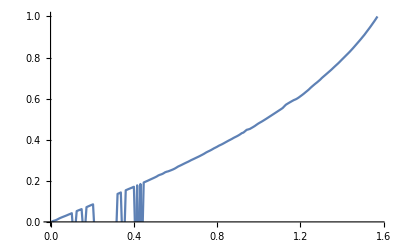

```mathematica
ListLinePlot[roughnessMap,PlotRange->{0,1}]
```

```mathematica
ta3[[129]]
ListInterpolation[ta3[[129]],{0,1}]
```

{4.99011×10^-7,0.000137635,0.000517598,0.00113956,0.00200219,0.0031036,0.00444146,0.00601289,0.00781458,0.00984274,0.0120932,0.0145613,0.017242,0.0201301,0.0232198,0.0265051,0.0299798,0.0336374,0.0374713,0.0414745,0.04564,0.0499608,0.0544295,0.059039,0.0637819,0.0686508,0.0736386,0.0787379,0.0839416,0.0892425,0.0946337,0.100045,0.105595,0.111216,0.1169,0.122641,0.128434,0.134273,0.140151,0.146064,0.152006,0.157994,0.163979,0.169978,0.175988,0.182002,0.188018,0.194031,0.200038,0.206035,0.21202,0.217987,0.223936,0.229863,0.235765,0.24164,0.247486,0.2533,0.259081,0.264827,0.270536,0.276206,0.281836,0.287425,0.292972}

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
taRoughnessFunctions=Table[ListInterpolation[ta3[[θ]],{0,1}],{θ,1,countX+1}];
```

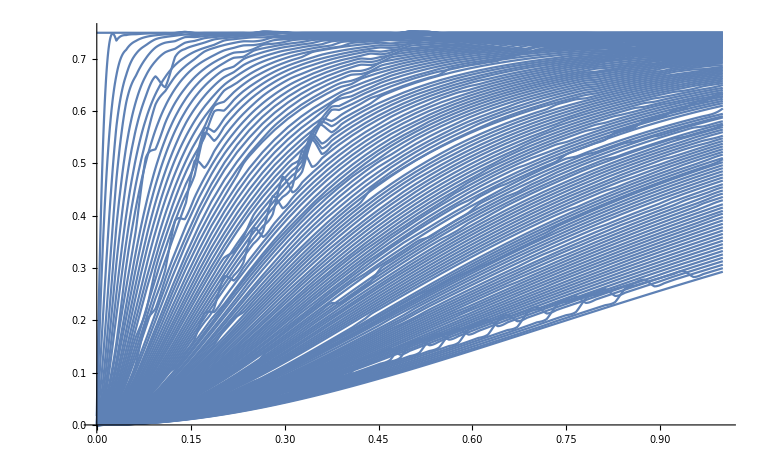

```mathematica
Plot[Table[taRoughnessFunctions[[x]][α],{x,1,countX+1}],{α,0,1},PlotRange->Full]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{0.00613592,0.00435388},{0.0122718,0.00798209},{0.0184078,0.0142397},{0.0245437,0.0201553},{0.0306796,0.0252147},{0.0368155,0.0300223},{0.0429515,0.0354113},{0.0490874,0.0404804},{0.0552233,-0.0658214},{0.0613592,0.051045},{0.0674952,0.0565301},{0.0736311,-0.0402626},{0.079767,-0.0439439},{0.0859029,0.0713379},{0.0920388,0.0768892},{0.0981748,0.0823181},{0.104311,-0.0585104},{0.110447,-0.0622605},{0.116583,-0.0661593},{0.122718,-0.0705562},{0.128854,-0.0744469},{0.13499,-0.0803063},{0.141126,-0.0817714},{0.147262,-0.0858957},{0.153398,-0.0856887},{0.159534,0.135034},{0.16567,0.140202},{0.171806,-0.102752},{0.177942,-0.106822},{0.184078,0.157011},{0.190214,0.16227},{0.19635,0.167385},{0.202485,0.172856},{0.208621,0.178433},{0.214757,-0.131462},{0.220893,0.189134},{0.227029,0.194696},{0.233165,0.200133},{0.239301,0.205986},{0.245437,0.211629},{0.251573,0.217418},{0.257709,0.22455},{0.263845,0.230028},{0.269981,0.23466},{0.276117,0.242498},{0.282252,0.245839},{0.288388,0.250602},{0.294524,0.255665},{0.30066,0.262018},{0.306796,0.269887},{0.312932,0.275454},{0.319068,0.281708},{0.325204,0.287863},{0.33134,0.293635},{0.337476,0.300281},{0.343612,0.306052},{0.349748,0.312021},{0.355884,0.317855},{0.362019,0.324275},{0.368155,0.330782},{0.374291,0.338491},{0.380427,0.34458},{0.386563,0.350833},{0.392699,0.358153},{0.398835,0.364227},{0.404971,0.371478},{0.411107,0.377125},{0.417243,0.38389},{0.423379,0.390831},{0.429515,0.397588},{0.435651,0.403923},{0.441786,0.411095},{0.447922,0.4172},{0.454058,0.424182},{0.460194,0.432875},{0.46633,0.43838},{0.472466,0.449222},{0.478602,0.452286},{0.484738,0.459453},{0.490874,0.466994},{0.49701,0.475944},{0.503146,0.483524},{0.509282,0.490576},{0.515418,0.498288},{0.521553,0.506292},{0.527689,0.514403},{0.533825,0.522467},{0.539961,0.530612},{0.546097,0.538741},{0.552233,0.546967},{0.558369,0.555424},{0.564505,0.569082},{0.570641,0.576769},{0.576777,0.584212},{0.582913,0.591416},{0.589049,0.596715},{0.595185,0.603977},{0.60132,0.613132},{0.607456,0.62233},{0.613592,0.632755},{0.619728,0.64284},{0.625864,0.654972},{0.632,0.665593},{0.638136,0.675708},{0.644272,0.686091},{0.650408,0.697668},{0.656544,0.708904},{0.66268,0.71963},{0.668816,0.73047},{0.674952,0.741436},{0.681087,0.753312},{0.687223,0.764731},{0.693359,0.776314},{0.699495,0.78915},{0.705631,0.801413},{0.711767,0.813951},{0.717903,0.826259},{0.724039,0.839728},{0.730175,0.85376},{0.736311,0.868149},{0.742447,0.882443},{0.748583,0.897328},{0.754719,0.912452},{0.760854,0.929299},{0.76699,0.945774},{0.773126,0.963088},{0.779262,0.980931},{0.785398,1.}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{0.999981,0.00435388},{0.999925,0.00798209},{0.999831,0.0142397},{0.999699,0.0201553},{0.999529,0.0252147},{0.999322,0.0300223},{0.999078,0.0354113},{0.998795,0.0404804},{0.998476,-0.0658214},{0.998118,0.051045},{0.997723,0.0565301},{0.99729,-0.0402626},{0.99682,-0.0439439},{0.996313,0.0713379},{0.995767,0.0768892},{0.995185,0.0823181},{0.994565,-0.0585104},{0.993907,-0.0622605},{0.993212,-0.0661593},{0.99248,-0.0705562},{0.99171,-0.0744469},{0.990903,-0.0803063},{0.990058,-0.0817714},{0.989177,-0.0858957},{0.988258,-0.0856887},{0.987301,0.135034},{0.986308,0.140202},{0.985278,-0.102752},{0.98421,-0.106822},{0.983105,0.157011},{0.981964,0.16227},{0.980785,0.167385},{0.97957,0.172856},{0.978317,0.178433},{0.977028,-0.131462},{0.975702,0.189134},{0.974339,0.194696},{0.97294,0.200133},{0.971504,0.205986},{0.970031,0.211629},{0.968522,0.217418},{0.966976,0.22455},{0.965394,0.230028},{0.963776,0.23466},{0.962121,0.242498},{0.960431,0.245839},{0.958703,0.250602},{0.95694,0.255665},{0.955141,0.262018},{0.953306,0.269887},{0.951435,0.275454},{0.949528,0.281708},{0.947586,0.287863},{0.945607,0.293635},{0.943593,0.300281},{0.941544,0.306052},{0.939459,0.312021},{0.937339,0.317855},{0.935184,0.324275},{0.932993,0.330782},{0.930767,0.338491},{0.928506,0.34458},{0.92621,0.350833},{0.92388,0.358153},{0.921514,0.364227},{0.919114,0.371478},{0.916679,0.377125},{0.91421,0.38389},{0.911706,0.390831},{0.909168,0.397588},{0.906596,0.403923},{0.903989,0.411095},{0.901349,0.4172},{0.898674,0.424182},{0.895966,0.432875},{0.893224,0.43838},{0.890449,0.449222},{0.88764,0.452286},{0.884797,0.459453},{0.881921,0.466994},{0.879012,0.475944},{0.87607,0.483524},{0.873095,0.490576},{0.870087,0.498288},{0.867046,0.506292},{0.863973,0.514403},{0.860867,0.522467},{0.857729,0.530612},{0.854558,0.538741},{0.851355,0.546967},{0.84812,0.555424},{0.844854,0.569082},{0.841555,0.576769},{0.838225,0.584212},{0.834863,0.591416},{0.83147,0.596715},{0.828045,0.603977},{0.824589,0.613132},{0.821103,0.62233},{0.817585,0.632755},{0.814036,0.64284},{0.810457,0.654972},{0.806848,0.665593},{0.803208,0.675708},{0.799537,0.686091},{0.795837,0.697668},{0.792107,0.708904},{0.788346,0.71963},{0.784557,0.73047},{0.780737,0.741436},{0.776888,0.753312},{0.77301,0.764731},{0.769103,0.776314},{0.765167,0.78915},{0.761202,0.801413},{0.757209,0.813951},{0.753187,0.826259},{0.749136,0.839728},{0.745058,0.85376},{0.740951,0.868149},{0.736817,0.882443},{0.732654,0.897328},{0.728464,0.912452},{0.724247,0.929299},{0.720003,0.945774},{0.715731,0.963088},{0.711432,0.980931},{0.707107,1.}}

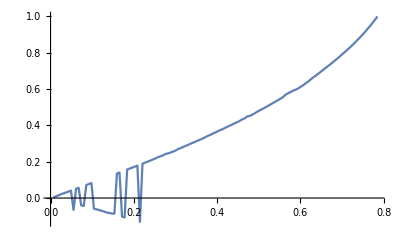

```mathematica
roughnessMap2=Table[{N[(θ0-1)/countX*π/4],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}]
roughnessMapCos2=Table[{N[Cos[(θ0-1)/countX*π/4]],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}]
ListLinePlot[roughnessMap2]
```

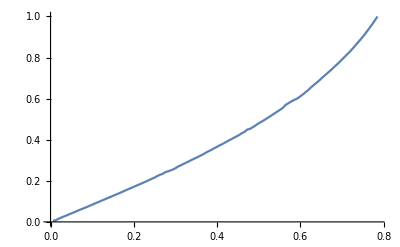

```mathematica
roughnessMap3={};
For[i=1,i<=countX,i++,If[roughnessMap2[[i]][[2]]≥0,AppendTo[roughnessMap3,roughnessMap2[[i]]]]]
ListLinePlot[roughnessMap3]
```

Let’s fit this...

{a→1.,b→0.813346,c→-0.605152,d→1.,e→-0.934716,f→1.}

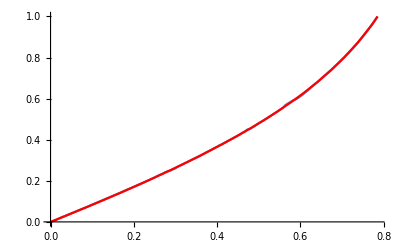

```mathematica
Clear[a,b,c,d,e,f,x,model]
model=0+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
model=(0+b*x+c*x^2)/(1+e*x+0*f*x^2);
FindFit[roughnessMap3,model,{a,b,c,d,e,f},x]
f2=Function[x,Evaluate[model/.FindFit[roughnessMap3,model,{a,b,c,d,e,f},x]]];
Show[ListLinePlot[roughnessMap3,PlotRange->{0,1}],Plot[f2[x],{x,0,π/2},PlotRange->{0,1},PlotStyle->Red]]
```

```mathematica
Sum[(f2[roughnessMap3[[i]][[1]]] - roughnessMap3[[i]][[2]])^2,{i,1,Length[roughnessMap3]}]
```

0.000208134

Let’s plot and compare with the 2D model

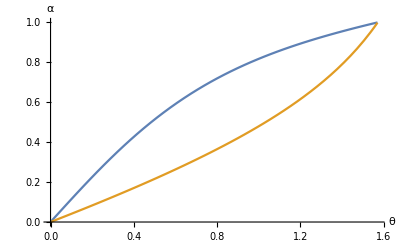

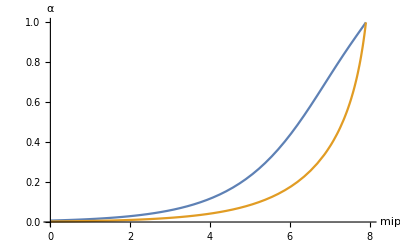

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
sqRoughnessFromMip[mip_]:=sqAlphaMu[mu[mip]] 
sqRoughnessFromMip3D[mip_]:=f2[mu[mip]]^2
sqRoughnessFromMip3D[mip_]:=f2[ArcCos[mu[mip]]]^2
(*Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]*)
Plot[{sqAlpha[θ/2]^(1/2),f2[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip3D[mip]},{mip,0,mipMax},PlotRange->{0,1},AxesLabel->{"mip","α"}]
```

Let’s map the inverse function now:

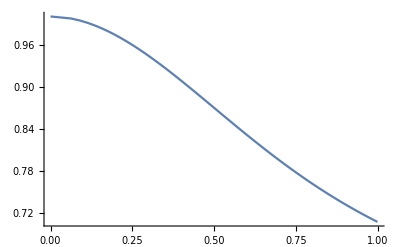

```mathematica
data=Table[{ N[f2[ArcCos[μ]]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}];
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(14.0653-3.07501 x+10.5404 x^2)/(14.0653-2.91058 x+19.3144 x^2)]

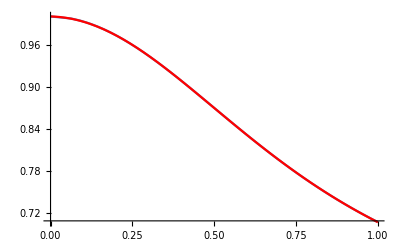

0.99934

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)
f3=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f3[x],{x,0,1},PlotStyle->Red]]
√2 f3[1]
```

Let’s plot and compare with the 2D model:

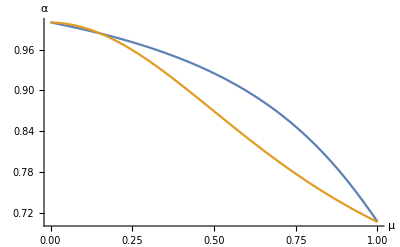

```mathematica
Plot[{f0[μ],f3[μ]},{μ,0,1},AxesLabel->{"μ","α"}]
```